```mathematica
f[x_]:=5Cos[2x+1]-3 x^2-5x+4
```

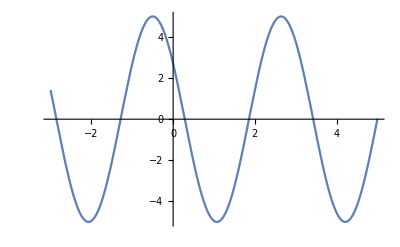

```mathematica
Plot[f[x], {x,-3,5}]
```

```mathematica
g[x_]:=3 x^2+5x-4
```

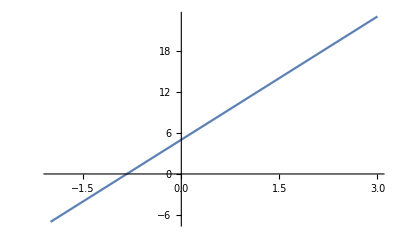

```mathematica
Plot[g'[x],{x,-2,3}]
```

```mathematica
x=-1;
e=0.001;
Do[
z=x;
x=g[x]//N;
If[Abs[z-x]<e,
Print["Решение x =",x//N," получено на ",i," шаге"];
Break[]],
{i,1,100}]
```

General::ovfl: Overflow occurred in computation.